```mathematica
f[x_]:=Sin[x]-x*Cos[x]
```

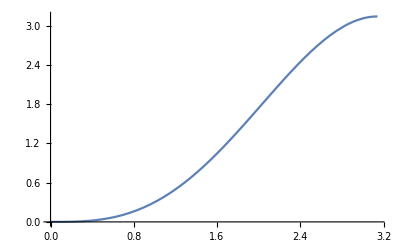

```mathematica
Plot[f[x],{x,0,Pi}]
```

```mathematica
f'[x]
```

x Sin[x]

```mathematica
NIntegrate[f[x],{x,0,Pi}]
```

```mathematica
4.000000000000005
NIntegrate[Sqrt[1 + (f'[x])^2], {x, 0, Pi}]
```

4.

4.6984

```mathematica
Integrate[Sqrt[1+(f'[x])^2], {x,0,Pi}]
```

∫_0^π √(1+x^2 Sin[x]^2)ⅆx

```mathematica
RevolutionPlot3D[f[x], {x, 0, Pi}]
```

-Graphics3D-

```mathematica
NIntegrate[2*Pi*f[x]*Sqrt[1 + (f'[x])^2], {x,0,Pi}]
```

41.1045